## Harmonic potential to sparse Einstein Hessian matrices Script to convert the harmonic limit prefactor from the potential mapping of displacement for each atom species in crystal to a sparse Hessian matrix.

```mathematica
Files;
```

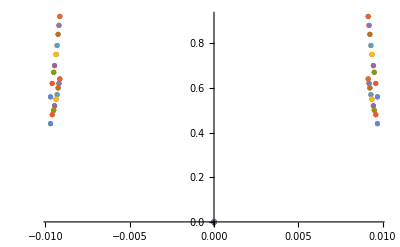

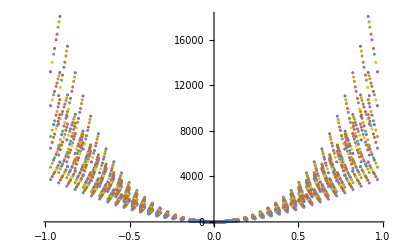

```mathematica
m={12.0107,91.224,1};
kB=1000*8.617332478*10^−5;K2meV=1000*8.617332478*10^−5;kjmol2evatom=1/(96.487*64);
e0perf={
-.67550095*10^3,-.67441442*10^3,-.67323280*10^3,-.67090290*10^3,-.66733277*10^3};
volperf={766.060,778.688,791.453,808.70835,822.656,846.590,862.257,885.289,912.673};
(*Data in*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/allvols"];
filesC={"C_4575","C_4600","C_4625","C_46583","C_4685_760","C_4730_1900","C_4759_2500","C_4801_3200","C_4850_3805","C_4575_110","C_4600_110","C_4625_110","C_46583_110","C_4685_760_110","C_4730_1900_110","C_4759_2500_110","C_4801_3200_110","C_4850_3805_110","C_4575_111","C_4600_111","C_4625_111","C_46583_111","C_4685_760_111","C_4730_1900_111","C_4759_2500_111","C_4801_3200_111","C_4850_3805_111"};
filesZr={"Zr_4575","Zr_4600","Zr_4625","Zr_46583","Zr_4685_760","Zr_4730_1900","Zr_4759_2500","Zr_4801_3200","Zr_4850_3805","Zr_4575_110","Zr_4600_110","Zr_4625_110","Zr_46583_110","Zr_4685_760_110","Zr_4730_1900_110","Zr_4759_2500_110","Zr_4801_3200_110","Zr_4850_3805_110","Zr_4575_111","Zr_4600_111","Zr_4625_111","Zr_46583_111","Zr_4685_760_111","Zr_4730_1900_111","Zr_4759_2500_111","zr_4801_3200_111","Zr_4850_3805_111"};
filesCh={"1.harm.C_4575","1.harm.C_4600","1.harm.C_4625","1.harm.C_46583","1.harm.C_4685_760","1.harm.C_4730_1900","1.harm.C_4759_2500","1.harm.C_4801_3200","1.harm.C_4850_3805","1.harm.C_4575_110","1.harm.C_4600_110","1.harm.C_4625_110","1.harm.C_46583_110","1.harm.C_4685_760_110","1.harm.C_4730_1900_110","1.harm.C_4759_2500_110","1.harm.C_4801_3200_110","1.harm.C_4850_3805_110","1.harm.C_4575_111","1.harm.C_4600_111","1.harm.C_4625_111","1.harm.C_46583_111","1.harm.C_4685_760_111","1.harm.C_4730_1900_111","1.harm.C_4759_2500_111","1.harm.C_4801_3200_111","1.harm.C_4850_3805_111"};
filesZrh={"1.harm.Zr_4575","1.harm.Zr_4600","1.harm.Zr_4625","1.harm.Zr_46583","1.harm.Zr_4685_760","1.harm.Zr_4730_1900","1.harm.Zr_4759_2500","1.harm.Zr_4801_3200","1.harm.Zr_4850_3805","1.harm.Zr_4575_110","1.harm.Zr_4600_110","1.harm.Zr_4625_110","1.harm.Zr_46583_110","1.harm.Zr_4685_760_110","1.harm.Zr_4730_1900_110","1.harm.Zr_4759_2500_110","1.harm.Zr_4801_3200_110","1.harm.Zr_4850_3805_110","1.harm.Zr_4575_111","1.harm.Zr_4600_111","1.harm.Zr_4625_111","1.harm.Zr_46583_111","1.harm.Zr_4685_760_111","1.harm.Zr_4730_1900_111","1.harm.Zr_4759_2500_111","1.harm.Zr_4801_3200_111","1.harm.Zr_4850_3805_111"};
Cdata=Table[ReadList[filesC[[i]],{Number, Number}],{i,1,27}];
Zrdata=Table[ReadList[filesZr[[i]],{Number, Number}],{i,1,27}];
hCdata=Table[ReadList[filesCh[[i]],{Number, Number}],{i,1,27}];
hZrdata=Table[ReadList[filesZrh[[i]],{Number, Number}],{i,1,27}];
Show[ListPlot@hCdata,ListPlot@hZrdata,PlotRange->All]
Show[ListPlot@Cdata,ListPlot@Zrdata,PlotRange->All]
```

```mathematica
Define and fit potentials;
(*Carbon*)
V[1,2,x_]:=Table[Fit[hCdata[[i]],{x^2},x],{i,1,27}]
V[1,4,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4},x],{i,1,27,9}]
V[1,6,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6},x],{i,1,27}]
V[1,8,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,27,9}]
V[1,10,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,27,9}]
V[1,12,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,27}]

V[2,2,x_]:=Table[Fit[hZrdata[[i]],{x^2},x],{i,1,27}]
V[2,4,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4},x],{i,1,27,9}]
V[2,6,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6},x],{i,1,27}]
V[2,8,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,27,9}]
V[2,10,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,27,9}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,27}]
GraphicsGrid[{{Show[Plot[Evaluate@{V[1,2,x][[1]],V[1,12,x][[1]],V[1,12,x][[10]],V[1,12,x][[11]]},{x,-1.2,1.2},PlotLegends->SwatchLegend[{"harmonic","100 anharmonic","110 anharmonic","111 anharmonic"}],PlotLabel->"Carbon potentials at 4.685Angstrom",AxesLabel->{"Angstrom","meV/atom"}],ImageSize->500],Show[Plot[Evaluate@{V[2,2,x][[1]],V[2,12,x][[1]],V[2,12,x][[10]],V[2,12,x][[11]]},{x,-1.2,1.2},PlotLegends->SwatchLegend[{"harmonic","100 anharmonic","110 anharmonic","111 anharmonic"}],PlotLabel->"Zirconium potentials at 4.685Angstrom",AxesLabel->{"Angstrom","meV/atom"}],ImageSize->500]}},ImageSize->1300]
```

-Graphics-

```mathematica
Cdata[[1]][[30;;37]]
Zrdata[[1]][[30;;37]]
```

{{-0.02745,5.74},{-0.0183,2.55},{-0.00915,0.64},{0,0},{0,0},{0.00915,0.64},{0.0183,2.55},{0.02745,5.74}}

{{-0.02745,8.25},{-0.0183,3.67},{-0.00915,0.92},{0,0},{0,0},{0.00915,0.92},{0.0183,3.67},{0.02745,8.25}}

```mathematica
Fit[Cdata[[1]][[33;;34]],{x^2},x]
Fit[Cdata[[1]][[32;;35]],{x^2},x]
Fit[Cdata[[1]][[31;;36]],{x^2},x]
Fit[Cdata[[1]][[30;;37]],{x^2},x]
Fit[Cdata[[1]][[29;;38]],{x^2},x]
```

0.

7644.3 x^2

7616.2 x^2

7617.49 x^2

7620.68 x^2

```mathematica
Units;
(*1 Bohr=0.529177208 Angstrom*)
(*1Hartree=27.211396 eV*)
ang2bohr=1/0.529177208;
ev2har=1/27.211396;
eVperAng2harperbohr=ev2har/ang2bohr;
eVperAng22harperbohr2=ev2har/ang2bohr/ang2bohr;
HarBohr=meVperAng22harperbohr2=0.001*ev2har/ang2bohr/ang2bohr;
```

```mathematica
Hessian code;
(*Define a function that generate a 2 element sparse Hessian matrix, based on dimension, zr einstein and c einstein values*)
sparseConditions[x_,y_,dim_,zr_,c_]:=Which[x==y&&x≤dim/2,zr,x==y&&x>dim/2,c,True,0]
sparseHessian[dim_,zr_,c_]:=Table[sparseConditions[i,j,dim,zr,c],{i,1,dim},{j,1,dim}]
(*Test with low dim matrix*)
sparseHessian[12,10,20]//MatrixForm;
sparseHessian[13,1,2]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2)

```mathematica
V[1,2,x][[1]][[1]]
V[2,2,x][[1]][[1]]
```

7644.3

10988.7

```mathematica
0.5Sqrt[2Table[V[1,2,x][[i]][[1]],{i,1,9}]/m[[1]]]
0.5Sqrt[2Table[V[2,2,x][[i]][[1]],{i,1,9}]/m[[2]]]
```

{17.839,17.4626,17.0858,16.5458,16.1489,15.5529,15.1707,14.7248,13.9526}

{7.76074,7.5489,7.33548,7.06796,6.84261,6.54769,6.37217,6.07233,5.71153}

```mathematica
Carbon and Zirconium input potential data;
(*Method 1) Read in Einstein oscillator PES, fit quadratic function, two times prefactor gives omega squared etc*)
(*Method 2), read QHA DOS - define Einstein oscillator frequency as either peak frequency, or as where the DOS integrates up to Natoms*3/2*)
Potential;
V[1,2,x][[1;;9]]
V[2,2,x][[1;;9]]
Forces;
cForce=D[V[1,2,x][[1;;9]],x]
zForce=D[V[2,2,x][[1;;9]],x]
Hessian;
cHessian=D[D[V[1,2,x][[1;;9]],x],x]
zHessian=D[D[V[2,2,x][[1;;9]],x],x]
```

{7644.3 x^2,7325.14 x^2,7012.42 x^2,6576.21 x^2,6264.46 x^2,5810.6 x^2,5528.52 x^2,5208.33 x^2,4676.37 x^2}

{10988.7 x^2,10397. x^2,9817.38 x^2,9114.39 x^2,8542.44 x^2,7821.96 x^2,7408.22 x^2,6727.43 x^2,5951.75 x^2}

{15288.6 x,14650.3 x,14024.8 x,13152.4 x,12528.9 x,11621.2 x,11057. x,10416.7 x,9352.75 x}

{21977.4 x,20794. x,19634.8 x,18228.8 x,17084.9 x,15643.9 x,14816.4 x,13454.9 x,11903.5 x}

{15288.6,14650.3,14024.8,13152.4,12528.9,11621.2,11057.,10416.7,9352.75}

{21977.4,20794.,19634.8,18228.8,17084.9,15643.9,14816.4,13454.9,11903.5}

```mathematica
Change units;
cHessian*HarBohr
zHessian*HarBohr
```

{0.157333,0.150764,0.144328,0.13535,0.128933,0.119592,0.113786,0.107196,0.0962478}

{0.226166,0.213988,0.202059,0.18759,0.175818,0.160989,0.152474,0.138462,0.122497}

```mathematica
Make a test Hessian for Zr1C1 system;
zrcHessian=Table[sparseHessian[6,zHessian[[i]]*HarBohr,cHessian[[i]]*HarBohr],{i,1,9}];
Table[zrcHessian[[i]]//MatrixForm,{i,1,9}]
```

{(0.226166 | 0 | 0 | 0 | 0 | 0
0 | 0.226166 | 0 | 0 | 0 | 0
0 | 0 | 0.226166 | 0 | 0 | 0
0 | 0 | 0 | 0.157333 | 0 | 0
0 | 0 | 0 | 0 | 0.157333 | 0
0 | 0 | 0 | 0 | 0 | 0.157333),(0.213988 | 0 | 0 | 0 | 0 | 0
0 | 0.213988 | 0 | 0 | 0 | 0
0 | 0 | 0.213988 | 0 | 0 | 0
0 | 0 | 0 | 0.150764 | 0 | 0
0 | 0 | 0 | 0 | 0.150764 | 0
0 | 0 | 0 | 0 | 0 | 0.150764),(0.202059 | 0 | 0 | 0 | 0 | 0
0 | 0.202059 | 0 | 0 | 0 | 0
0 | 0 | 0.202059 | 0 | 0 | 0
0 | 0 | 0 | 0.144328 | 0 | 0
0 | 0 | 0 | 0 | 0.144328 | 0
0 | 0 | 0 | 0 | 0 | 0.144328),(0.18759 | 0 | 0 | 0 | 0 | 0
0 | 0.18759 | 0 | 0 | 0 | 0
0 | 0 | 0.18759 | 0 | 0 | 0
0 | 0 | 0 | 0.13535 | 0 | 0
0 | 0 | 0 | 0 | 0.13535 | 0
0 | 0 | 0 | 0 | 0 | 0.13535),(0.175818 | 0 | 0 | 0 | 0 | 0
0 | 0.175818 | 0 | 0 | 0 | 0
0 | 0 | 0.175818 | 0 | 0 | 0
0 | 0 | 0 | 0.128933 | 0 | 0
0 | 0 | 0 | 0 | 0.128933 | 0
0 | 0 | 0 | 0 | 0 | 0.128933),(0.160989 | 0 | 0 | 0 | 0 | 0
0 | 0.160989 | 0 | 0 | 0 | 0
0 | 0 | 0.160989 | 0 | 0 | 0
0 | 0 | 0 | 0.119592 | 0 | 0
0 | 0 | 0 | 0 | 0.119592 | 0
0 | 0 | 0 | 0 | 0 | 0.119592),(0.152474 | 0 | 0 | 0 | 0 | 0
0 | 0.152474 | 0 | 0 | 0 | 0
0 | 0 | 0.152474 | 0 | 0 | 0
0 | 0 | 0 | 0.113786 | 0 | 0
0 | 0 | 0 | 0 | 0.113786 | 0
0 | 0 | 0 | 0 | 0 | 0.113786),(0.138462 | 0 | 0 | 0 | 0 | 0
0 | 0.138462 | 0 | 0 | 0 | 0
0 | 0 | 0.138462 | 0 | 0 | 0
0 | 0 | 0 | 0.107196 | 0 | 0
0 | 0 | 0 | 0 | 0.107196 | 0
0 | 0 | 0 | 0 | 0 | 0.107196),(0.122497 | 0 | 0 | 0 | 0 | 0
0 | 0.122497 | 0 | 0 | 0 | 0
0 | 0 | 0.122497 | 0 | 0 | 0
0 | 0 | 0 | 0.0962478 | 0 | 0
0 | 0 | 0 | 0 | 0.0962478 | 0
0 | 0 | 0 | 0 | 0 | 0.0962478)}

```mathematica
Modes/Atoms per supercell;
(*2x2x2*)
3*8*2^3
(*3x3x3*)
3*8*3^3
(*4x4x4*)
3*8*4^3
```

192

648

1536

```mathematica
1536^2
```

2359296

```mathematica
Hessian for Zr32C32;
zrc192harmonicHessian4685=sparseHessian[192,zHessian[[5]]*HarBohr,cHessian[[5]]*HarBohr];
zrc192harmonicHessian4730=sparseHessian[192,zHessian[[6]]*HarBohr,cHessian[[6]]*HarBohr];
zrc192harmonicHessian4759=sparseHessian[192,zHessian[[7]]*HarBohr,cHessian[[7]]*HarBohr];
zrc192harmonicHessian4801=sparseHessian[192,zHessian[[8]]*HarBohr,cHessian[[8]]*HarBohr];zrc192harmonicHessian4850=sparseHessian[192,zHessian[[9]]*HarBohr,cHessian[[9]]*HarBohr];
Export["zrc192harmonicHessian4685.dat",zrc192harmonicHessian4685]
Export["zrc192harmonicHessian4730.dat",zrc192harmonicHessian4730]
Export["zrc192harmonicHessian4759.dat",zrc192harmonicHessian4759]
Export["zrc192harmonicHessian4801.dat",zrc192harmonicHessian4801]
Export["zrc192harmonicHessian4850.dat",zrc192harmonicHessian4850]
```

zrc192harmonicHessian4685.dat

zrc192harmonicHessian4730.dat

zrc192harmonicHessian4759.dat

zrc192harmonicHessian4801.dat

zrc192harmonicHessian4850.dat

```mathematica
Hessian for Zr108C108;
zrc648harmonicHessian4685=sparseHessian[648,zHessian[[5]]*HarBohr,cHessian[[5]]*HarBohr];
Export["zrc648harmonicHessian4685.dat",zrc648harmonicHessian4685]
```

zrc648harmonicHessian4685.dat

```mathematica
Hessian for Zr256C256;
zrc1536harmonicHessian4685=sparseHessian[1536,zHessian[[5]]*HarBohr,cHessian[[5]]*HarBohr];
Export["zrc1536harmonicHessian4685.dat",zrc1536harmonicHessian4685]
```

zrc1536harmonicHessian4685.dat

```mathematica
(*Import TI between 4.685Angstrom Einstein Hessian and 4.685Angstrom MEAM *)
(*T=300 760 1900 2500 3200 3805*)
```

```mathematica
(*SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis"];
data=ReadList["lambda_dudl_4685Ang_normalMEAM_Eistein_comparison_6T",Number];
dataFahMEAM=ReadList["Fah_MEAM_normal_4685",Number];
dataFahEinstein=ReadList["Fah_Einstein_4685",Number];
lambdaData=Transpose[Partition[Flatten@data,3]][[1]];
dudlHarmonic=Transpose[Partition[Flatten@data,3]][[2]];
dudlEinstein=Transpose[Partition[Flatten@data,3]][[3]];
dataFahMeanVal={-3.83,-7.66,-12.40,-15.06,-18.81,-23.46};
(*Plot dUdL for harmonic and Einstein starting point*)
ListPlot[dudlHarmonic]
ListPlot[dudlEinstein]*)
```

```mathematica
(*(*Plot dUdL for harmonic and Einstein starting point*)

"Normel harmonic to anharmonic dUdL:"
Show[ListPlot[Transpose@{lambdaData,dudlHarmonic}],ListPlot[Partition[Transpose@{lambdaData,dudlHarmonic},11],Joined->True]]

"Einstein harmonic to anharmonic dUdL:"
Show[ListPlot[Transpose@{lambdaData,dudlEinstein}],ListPlot[Partition[Transpose@{lambdaData,dudlEinstein},11],Joined->True]]
{dataFahMEAM,dataFahEinstein,dataFahMeanVal}//TableForm
ListPlot@{dataFahMEAM,dataFahEinstein,dataFahMeanVal}*)
```